# Practical Test

## Name: Puranjyoti Bera 20201043

## Q.1) Plot the fifth root of unity

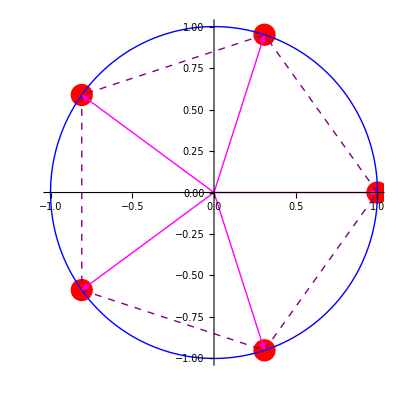

```mathematica
a:=ListPlot[Table[{Re[Exp[2*Pi*I*n/5]], Im[Exp[2*Pi*I*n/5]]},{n,0,4}],
AspectRatio-> Automatic,PlotStyle->{Red,PointSize[0.04]}];
b:=ParametricPlot[{Cos[t],Sin[t]},{t,0,2*Pi},PlotStyle->{Thick,Blue}];
c:=Table[Graphics[{Thick,Magenta,Arrow[{{0,0},{Re[Exp[2*Pi*I*n/5]],Im[Exp[2*Pi*I*n/5]]}}]}],{n,0,4}];
d:=Table[Graphics[{Thick,Dashed,Purple,Line[{{Re[Exp[2*Pi*I*n/5]],Im[Exp[2*Pi*I*n/5]]},{Re[Exp[2*Pi*I(n+1)/5]],Im[Exp[2*Pi*I*(n+1)/5]]}}]}],{n,0,4}];

Show[a,b,c,d,PlotRange->1.25]
```

## Q.2) Plot the open disk:

```mathematica
ClearAll
```

ClearAll

The open disk Re(z) >=1/2 is given by the figure

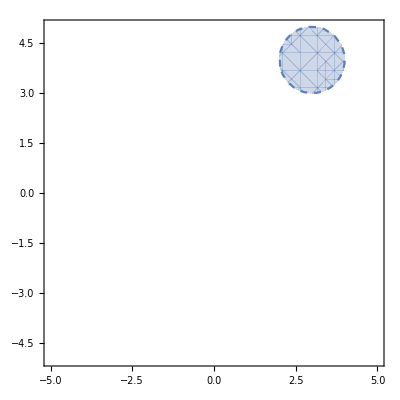

The image of the open disk Re(z) >=1/2 under the function f(z)= (1+2 ⅈ)+4 z is given by the figure

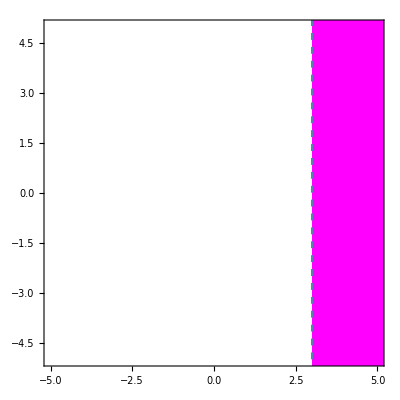

```mathematica
Print["The open disk Re(z) >=1/2 is given by the figure"];
RegionPlot[Abs[x+I y-3-4I]<1,{x,-10,10},{y,-10,10},BoundaryStyle->Dashed,PlotRange->5,Axes->True]
f[z_]:= 4z +1+2I;
w=u+I v;
root:=z /. ComplexExpand[Solve[f[z]==w,z]];
Print["The image of the open disk Re(z) >=1/2 under the function f(z)= ",f[z]," is given by the figure"];
RegionPlot[Re[root[[1]]]≥1/2,{u,-10,10},{v,-10,10},PlotStyle->Magenta,BoundaryStyle->Dashed,PlotRange->5,Axes->True]
```

## Q.3)

The  the horizontal lines y=1,-1/2,1/2,1 are given by the figure

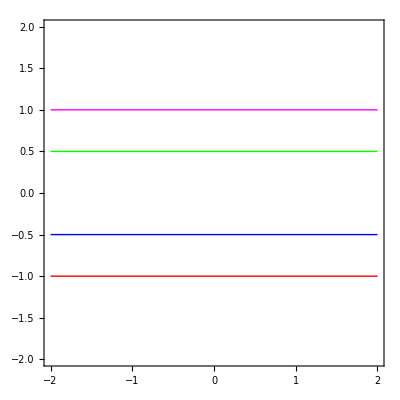

The image of the  the horizontal lines y=1,-1/2,1/2,1 under the function f(z)=1/z is given by the figure

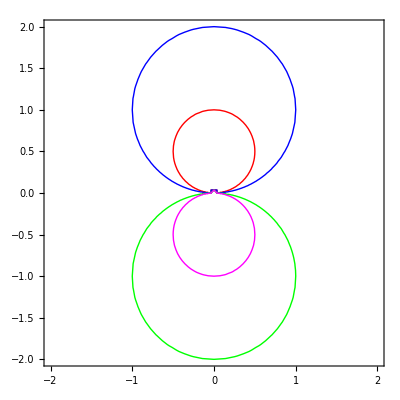

```mathematica
Print["The  the horizontal lines y=1,-1/2,1/2,1 are given by the figure"];
grid:={-1,-1/2,1/2,1};
ycolour:={Red,Blue,Green,Magenta};

Show[Table[ContourPlot[Im[x+I y]==grid[[i]],{x,-2,2},{y,-2,2},ContourStyle->{Thick,ycolour[[i]]},Axes->True],{i,1,4}]]
f[z_]:=1/z;
w=u+I v;
root:=z/.ComplexExpand[Solve[f[z]==w,z]];
Print["The image of the  the horizontal lines y=1,-1/2,1/2,1 under the function f(z)=",f[z]," is given by the figure"];
Show[Table[ContourPlot[Im[root[[1]]]==grid[[i]],{u,-2,2},{v,-2,2},ContourStyle->{Thick,ycolour[[i]]},Axes->True],{i,1,4}]]//Quiet
```

## Q.5)Laurent Series:

The given function is f(z) = 1/((-3+z) (-1+z))

The roots of the denominator 2+z-z^2 == 0 are {1,3}

The Talor series expansion of the function f is valid in the disk |z|>1 and Laurent series expansion of the function f is valid in the annulus 1<|z|<2 and |z|>2. These three domains are illustrated in the following figure :

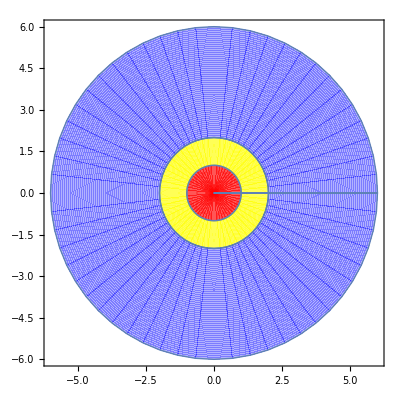

The Talor series expansion of the function f is valid in the disk |z|<1 is given by f(z) = 1/3+(4 z)/9+(13 z^2)/27+(40 z^3)/81+(121 z^4)/243+(364 z^5)/729+(1093 z^6)/2187+(3280 z^7)/6561+(9841 z^8)/19683+(29524 z^9)/59049+(88573 z^10)/177147+O[z]^11

The partial fraction gives f(z) = 1/(2 (-3+z))-1/(2 (-1+z))

The Laurent series expansion of the function f in the annulus 1<|z|<2 is given by f(z) = (-1-z-z^2-z^3-z^4-z^5-z^6-z^7-z^8-z^9-z^10+O[z]^11)+(1/z+3/z^2+9/z^3+27/z^4+81/z^5+243/z^6+729/z^7+2187/z^8+6561/z^9+19683/z^10+O[1/z]^11)

The Laurent series expansion of the function f in the annulus |z|>2 is given by f(z) = (1/z)^2+4/z^3+13/z^4+40/z^5+121/z^6+364/z^7+1093/z^8+3280/z^9+9841/z^10+O[1/z]^11

```mathematica
f[z_]:=1/((z-1)(z-3));
Print["The given function is f(z) = ",f[z]];
Print["The roots of the denominator 2+z-z^2 == 0 are ",z/.Solve[(z-1)(z-3)==0,z]];
Print["The Talor series expansion of the function f is valid in the disk |z|>1 and Laurent series expansion of the function f is valid in the annulus 1<|z|<2 and |z|>2. These three domains are illustrated in the following figure :"]
Show[ParametricPlot[{r*Cos[t],r*Sin[t]},{r,0,1},{t,0,2*Pi},PlotStyle-> Red,Mesh-> None],ParametricPlot[{r*Cos[t],r*Sin[t]},{r,1,2},{t,0,2*Pi},PlotStyle-> Yellow,Mesh-> None],ParametricPlot[{r*Cos[t],r*Sin[t]},{r,2,6},{t,0,2*Pi},PlotStyle-> Blue,Mesh-> None],PlotRange-> 4]
Print["The Talor series expansion of the function f is valid in the disk |z|<1 is given by f(z) = ",Series[f[z],{z,0,10}]];
Print["The partial fraction gives f(z) = ",Apart[f[z]]];
Print["The Laurent series expansion of the function f in the annulus 1<|z|<2 is given by f(z) = ",Series[1/(z-1),{z,0,10}]+Series[1/(z-3),{z,Infinity,10}]];
Print["The Laurent series expansion of the function f in the annulus |z|>2 is given by f(z) = ",Series[f[z],{z,Infinity,10}]];
```